Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

4 - 18 Temperature T(x,y) in plates
Find the temperature distribution T(x,y) and the complex potential in the given thin metal plate whose faces are insulated and whose edges are kept at the indicated temperatures or are insulated as shown.

5. Sector

```mathematica
Clear["Global`*"]
```

```mathematica
kru=RGBColor[0.392,0.823,0.98];
```

```mathematica
Graphics[{{Line[{{0,0},{0,1}}]},{Line[{{0,0},{1,0}}]},{Line[{{0,0},{0.75,-0.75}}]},{Line[{{0,0},{1,0}}]},{Line[{{0,0},{0.75,0.75}}]},{kru,Opacity[0.6],Polygon[{{0,0},{0.55,-0.55},{0.6,-0.2},{0.55,0},{0.6,0.2},{0.55,0.55},{0,0}}]},{Text[Style["T=20℃",Medium],{0.2,0.3},Automatic,{0.6,0.6}]},{Text[Style["T=-20℃",Medium],{0.2,-0.3},Automatic,{0.6,-0.6}]},{Circle[{0,0},0.18,{-π/4,π/4}]},{Text[Style["45̊",Medium],{0.3,0.1}]},{Text[Style["45̊",Medium],{0.3,-0.1}]}},ImageSize->100]
```

-Graphics-

According to example 3 on p. 768 the answer will be in the form

```mathematica
cnr[x_,y_]=a θ +b
```

b+a θ

Looking at the geometry of the figure, the T_1 leg has angle -π/4, and the T_2 leg has angle π/4, implying that the boundary conditions are seen in

a (-π/4)+b==T_2 , and a( π/4) +b==T_1

because of the Arg values of the two T lines, -π/4 and π/4, which suggests

```mathematica
Solve[-a π/4+b==-20&&a π/4+b==20,{a,b}]
```

{{a→80/π,b→0}}

putting this back into the starting equation

```mathematica
Simplify[cnr[x,y]/.{a->80/π,b->0}]
```

(80 θ)/π

According to example 3 on p. 760, θ=ArcTan[y/x]

This is not the complete answer. I need the harmonic conjugate of this expression in order to get the complex potential, which is equal to Φ[x,y]+ⅈ Ψ[x,y]. This is simple as pie using the identity discussed in problem 15 below and consists of

```mathematica
(80θ)/π=80Arg[z]
```

and the complex potential is

```mathematica
Φ +ⅈ Ψ = -(ⅈ 80)/π Log[z]
```

But maybe I would rather find a different harmonic conjugate to go with my Φ function. Then with help from utube’s MathSorcerer in https://www.youtube.com/watch?v=tWX8YwKfd_k I look for v such that f = u + ⅈ v is analytic. First I need the partials of u:

```mathematica
u[x_,y_]=80/π ArcTan[y/x]
```

(80 ArcTan[y/x])/π

```mathematica
D[u[x,y],x]
```

-(80 y)/(π x^2 (1+y^2/x^2))

```mathematica
D[u[x,y],y]
```

80/(π x (1+y^2/x^2))

Since I’m trying to build this to be analytic, I use Cauchy-Riemann, D[v[x,y],y] = D[u[x,y],x] and -D[v[x,y],x] = D[u[x,y],y]. Using the first of the pair of C-R,

```mathematica
D[v[x,y],y]=D[u[x,y],x]=-(80 y)/(π x^2 (1+y^2/x^2))
```

So to find the aspect of v which satisfies the y branch I can integrate this partial derivative with respect to y

```mathematica
∫-(80 y)/(π x^2 (1+y^2/x^2))ⅆy
```

-(40 Log[x^2+y^2])/π

And because I integrated with respect to ⅆy, I need to add an unknown function of x, getting

```mathematica
-(40 Log[x^2+y^2])/π+g[x]
```

g[x]-(40 Log[x^2+y^2])/π

as a candidate v function with symbolic x hang-on function. At this point I can differentiate the last expression with respect to x to look for the x aspect of v

```mathematica
D[g[x]-(40 Log[x^2+y^2])/π,x]
```

-(80 x)/(π (x^2+y^2))+g'[x]

and the above quantity can be set equal to the partial of v with respect to x which I already have (which is equal to the negative of the partial derivative of u with respect to y), thus

```mathematica
-D[v[x,y],x]=-80/(π x (1+y^2/x^2))=-(80 x)/(π (x^2+y^2))+g'[x]
```

Leaving the negative signs in now for consistency

```mathematica
Solve[-80/(π x (1+y^2/x^2))==-(80 x)/(π (x^2+y^2))+g'[x],g'[x]]
```

{{g'[x]→0}}

Here I assert that integrating at this point produces g[x] equal to C, and I decide to set C=0.

And from here I should be able to build the v function from

```mathematica
v[x_,y_]=Simplify[-(40 Log[x^2+y^2])/π]
```

-(40 Log[x^2+y^2])/π

The above expression being only v, the entire complex potential should be equal to

```mathematica
FullSimplify[80/π ArcTan[y/x]+ⅈ ((40 Log[x^2+y^2])/π)]
```

(80 ArcTan[y/x]+40 ⅈ Log[x^2+y^2])/π

```mathematica
PossibleZeroQ[(80 ArcTan[y/x]+40 ⅈ Log[x^2+y^2])/π-((-80ⅈ)/π Log[x+ⅈ y])]
```

False

Oh well, I didn’t expect to come up with the same Ψ as the text. To defend my answer (which is less elegant looking than the text’s) I need to verify that Φ and Ψ are analytic.

```mathematica
PossibleZeroQ[D[u[x,y],x]-D[v[x,y],y]]
```

True

```mathematica
PossibleZeroQ[D[u[x,y],y]+D[v[x,y],x]]
```

True

So according to numbered line (2) on p. 760, Φ and Ψ together make up a complex potential, the thing I was looking for. The yellow cell above matches (in intent though not in content) the text answer. Using the mechanical process of the math sorcerer, I am likely to come up with rather rough looking though hopefully defensible results.

7. Corner

```mathematica
Clear["Global`*"]
```

```mathematica
kru=RGBColor[0.392,0.823,0.98];
```

```mathematica
Graphics[{{Line[{{0,0},{0,1}}]},{Line[{{0,0},{1,0}}]},{kru,Opacity[0.6],Polygon[{{0,0},{0.6,0},{0.65,0.15},{0.6,0.2},{0.55,0.23},{0.45,0.55},{0.3,0.6},{0.12,0.66},{0,0.7},{0,0}}]},{Text[Style["T=T_2",Medium],{-0.08,0.3},Automatic,{-0.01,1}]},{Text[Style["T=T_1",Medium],{0.3,-0.12}]},{Text[Style["x",Medium],{1,-0.1}]},{Text[Style["y",Medium],{-0.08,0.95}]}},ImageSize->100]
```

-Graphics-

According to example 3 on p. 768 the answer will be in the form

```mathematica
tee[x_,y_]=a θ +b
```

b+a θ

Looking at the geometry of the figure, the T_1 leg has angle 0, and the T_2 leg has angle π/2, implying that the boundary conditions are seen in

```mathematica
a π/2+b==Subscript[T, 2] , and  a(0) +b==Subscript[T, 1]
```

because of the Arg values of the two T lines, π/2 and 0, which suggests

```mathematica
Solve[a π/2+b==Subscript[T, 2]&&b==Subscript[T, 1],{a,b}]
```

{{a→-(2 (T_1-T_2))/π,b→T_1}}

putting this back into the starting equation

```mathematica
Simplify[tee[x,y]/.{a->-(2 (Subscript[T, 1]-Subscript[T, 2]))/π,b->Subscript[T, 1]}]
```

T_1-(2 θ (T_1-T_2))/π

substituting ArcTan[y/x] for θ and rearranging gives the expression

```mathematica
Subscript[T, 1]+2/π(Subscript[T, 2]-Subscript[T, 1])ArcTan[y/x]
```

Though it matches the text, this is not the complete answer. I need the harmonic conjugate of this expression in order to get the complex potential, which is equal to Φ[x,y]+ⅈ Ψ[x,y]. This is just as easy as in problem 5.

```mathematica
Φ +ⅈ Ψ = Subscript[T, 1]+(-ⅈ 2)/π(Subscript[T, 2]-Subscript[T, 1])Log[z]
```

There is something to consider about the above expression. In the first green cell it is seen that the ArcTan, or Arg component is separate from the T_1 component. The T_1 component will be the Φ and the component containing the Arg device will be the Ψ. So when the -ⅈ is applied, it is only applied to the component with the Arg.

Now I will crank through the process of generating a complex potential mechanically. So with another helping hand from utube’s MathSorcerer in https://www.youtube.com/watch?v=tWX8YwKfd_k I look for v such that f = u + ⅈ v is analytic. First I need the partials of u:

```mathematica
u[x_,y_]=Subscript[T, 1]+2/π(Subscript[T, 2]-Subscript[T, 1])ArcTan[y/x]
```

T_1+(2 ArcTan[y/x] (-T_1+T_2))/π

```mathematica
D[u[x,y],x]
```

-(2 y (-T_1+T_2))/(π x^2 (1+y^2/x^2))

```mathematica
D[u[x,y],y]
```

(2 (-T_1+T_2))/(π x (1+y^2/x^2))

Since I’m trying to build this to be analytic, I use Cauchy-Riemann, D[v[x,y],y] = D[u[x,y],x] and -D[v[x,y],x] = D[u[x,y],y]. Using the first of the pair of C-R,

```mathematica
D[v[x,y],y]=-(2 y (-Subscript[T, 1]+Subscript[T, 2]))/(π x^2 (1+y^2/x^2))
```

So to find the aspect of v which satisfies the y branch I can integrate this partial derivative with respect to y

```mathematica
∫-(2 y (-Subscript[T, 1]+Subscript[T, 2]))/(π x^2 (1+y^2/x^2))ⅆy
```

(Log[x^2+y^2] (T_1-T_2))/π

And because I integrated with respect to dy, I need to add an unknown function of x, getting

```mathematica
(Log[x^2+y^2] (Subscript[T, 1]-Subscript[T, 2]))/π+g[x]
```

g[x]+(Log[x^2+y^2] (T_1-T_2))/π

as a candidate v function with symbolic x hang-on function. At this point I can differentiate the last expression with respect to x to look for the x aspect of v

```mathematica
D[g[x]+(Log[x^2+y^2] (Subscript[T, 1]-Subscript[T, 2]))/π,x]
```

(2 x (T_1-T_2))/(π (x^2+y^2))+g'[x]

and the above quantity can be set equal to the partial of v with respect to x which I already have (which is equal to the negative of the partial derivative of u with respect to y), thus

```mathematica
-D[v[x,y],x]=-(2 (-Subscript[T, 1]+Subscript[T, 2]))/(π x (1+y^2/x^2))=(2 x (Subscript[T, 1]-Subscript[T, 2]))/(π (x^2+y^2))+g'[x]
```

Leaving the negative sign in for consistency

```mathematica
Solve[-(2 (-Subscript[T, 1]+Subscript[T, 2]))/(π x (1+y^2/x^2))==(2 x (Subscript[T, 1]-Subscript[T, 2]))/(π (x^2+y^2))+g'[x],g'[x]]
```

{{g'[x]→0}}

Here I assert that integrating at this point produces g[x] equal to simply C, and I decide to set C=0.

And from here I should be able to build the v function from

```mathematica
v[x_,y_]=FullSimplify[(Log[x^2+y^2] (Subscript[T, 1]-Subscript[T, 2]))/π]
```

(Log[x^2+y^2] (T_1-T_2))/π

And the entire complex potential should be equal to

```mathematica
Subscript[T, 1]+2/π(Subscript[T, 2]-Subscript[T, 1])ArcTan[y/x]+ⅈ((Log[x^2+y^2] (Subscript[T, 1]-Subscript[T, 2]))/π)
```

T_1+(ⅈ Log[x^2+y^2] (T_1-T_2))/π+(2 ArcTan[y/x] (-T_1+T_2))/π

Again the Ψ is much different from the text. To defend my answer I need to verify that Φ and Ψ are analytic.

```mathematica
PossibleZeroQ[D[u[x,y],x]-D[v[x,y],y]]
```

True

```mathematica
PossibleZeroQ[D[u[x,y],y]+D[v[x,y],x]]
```

True

So according to numbered line (2) on p. 760, Φ and Ψ together make up a complex potential, the thing I was looking for. The yellow cell above matches (in intent though not in content) the text answer.

9. Upper half-plane

```mathematica
Clear["Global`*"]
```

```mathematica
kru=RGBColor[0.392,0.823,0.98];
innerbw=RGBColor[.97,.97,.994];
```

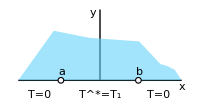

```mathematica
Graphics[{{Line[{{1.15,0},{1.15,1}}]},{Line[{{0,0},{2.3,0}}]},{kru,Opacity[0.6],Polygon[{{0,0},{2.3,0},{2.2,0.15},{2.1,0.2},{2,0.23},{1.7,0.55},{1,0.6},{0.7,0.66},{0.5,0.7},{0,0}}]},{Text[Style["T^*=T_1",Medium],{1.15,-0.2}]},{Text[Style["T=0",Medium],{0.3,-0.2}]},{Text[Style["x",Medium],{2.3,-0.1}]},{Text[Style["y",Medium],{1.05,0.95}]},{EdgeForm[Directive[Black]],innerbw,Disk[{0.6,0},0.04]},{EdgeForm[Directive[Black]],innerbw,Disk[{1.69,0},0.04]},{Text[Style["T=0",Medium],{1.97,-0.2}]},{Text[Style["a",Medium],{0.61,.12}]},{Text[Style["b",Medium],{1.7,.12}]}},ImageSize->200]
```

This problem is basically the same as example 3 on p. 760, applying a heat perspective instead of an electrostatic perspective. From there, the solution equation looks like

```mathematica
Φ[x,y]=a+b Arg[z]
```

Note here that the algebraic a and b in the above expression are unrelated to the points in the sketch.

There are three phi functions, according to location, call them Φ_1, Φ_2, and Φ_3, separated by the points a and b. The two quantities Φ_1 and Φ_3 both have the π angle, the same as Φ_2. However, because they have zero temperature, their contributions disappear, leaving only Φ_2, which has both magnitude and angle. So the equation for phi reduces to simply

```mathematica
0+b Arg[z] =Subscript[Φ, 2]=Subscript[T, 1]/π θ=Subscript[T, 1]/π ArcTan[y/x]
```

The angle y/x has an interpretation here, because in this problem the x interval is subdivided. It is necessary to get rid of everything that does not describe T_1, which is all x beyond the T_1 segment. To do this can look like the following:

```mathematica
Subscript[T, 1]/π(ArcTan[y/(x-b)]-ArcTan[y/(x-a)])
```

Now heading toward the complex potential form. The part in parentheses above could be treated like in problem 15 below, since it is the Arg,

```mathematica
Φ+ⅈΨ=(ⅈ Subscript[T, 1])/π(Log[y/(x-b)]-Log[y/(x-a)])=(ⅈ Subscript[T, 1])/π(Log[y/(x-b)]+Log[(x-a)/y])=(ⅈ Subscript[T, 1])/π(Log[(x-a)/(x-b)])
```

When substituting ⅈ Log for Arg it is necessary to remember the minus sign.

11. Upper half-plane

```mathematica
Clear["Global`*"]
```

```mathematica
kru=RGBColor[0.392,0.823,0.98];
innerbw=RGBColor[.97,.97,.994];
```

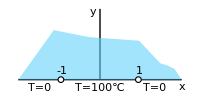

```mathematica
Graphics[{{Line[{{1.15,0},{1.15,1}}]},{Line[{{0,0},{2.3,0}}]},{kru,Opacity[0.6],Polygon[{{0,0},{2.3,0},{2.2,0.15},{2.1,0.2},{2,0.23},{1.7,0.55},{1,0.6},{0.7,0.66},{0.5,0.7},{0,0}}]},{Text[Style["T=100℃",Medium],{1.15,-0.12}]},{Text[Style["T=0",Medium],{0.3,-0.12}]},{Text[Style["x",Medium],{2.3,-0.1}]},{Text[Style["y",Medium],{1.05,0.95}]},{EdgeForm[Directive[Black]],innerbw,Disk[{0.6,0},0.04]},{EdgeForm[Directive[Black]],innerbw,Disk[{1.69,0},0.04]},{Text[Style["T=0",Medium],{1.92,-0.12}]},{Text[Style["-1",Medium],{0.61,.12}]},{Text[Style["1",Medium],{1.7,.12}]}},ImageSize->200]
```

This is apparently like problem 9, except that now the points a and b are assigned specific values. Again I look to example 3 on p. 760, applying a heat perspective instead of an electrostatic perspective. From there, the solution equation is

```mathematica
Φ[x,y]=a+b Arg[z]
```

Here there are no labels on the sketch to confuse with the variables in the equation above.

There are again three phi functions, according to location, call them Φ_1, Φ_2, and Φ_3, separated by the points {-1,0} and {1,0}. The two quantities Φ_1 and Φ_3 both have the π angle, the same as Φ_2. However, because they have zero temperature, their contributions disappear, leaving only Φ_2, which has both magnitude and angle. So the equation for phi reduces to simply

```mathematica
0+b Arg[z] =Subscript[Φ, 2]=Subscript[T, 1]/π θ=Subscript[T, 1]/π Arg[z]=100/π Arg[z]
```

The axis is clearly labeled x, but since y is equal to zero, the expression above is still true. And, applying the point location elimination,

```mathematica
Φ=100/π(Arg[z-1]-Arg[z-(-1)])=100/π(Arg[z-1]-Arg[z+1])
```

Now it is time to push for the complex potential expression, and as in problem 15, and retaining the z nomenclature to agree with text,

```mathematica
Φ+ⅈΨ=(ⅈ 100)/π(-Log[z-1]+Log[z+1])=(ⅈ 100)/π(Log[z+1]/Log[z-1])
```

13. Corner

```mathematica
Clear["Global`*"]
```

```mathematica
kru=RGBColor[0.392,0.823,0.98];
```

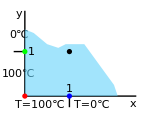

```mathematica
Graphics[{{Line[{{0,0},{0,1.15}}]},{Line[{{0,0},{1.5,0}}]},{Line[{{0.6,0},{0.6,-0.15}}]},{Line[{{0,0.6},{-0.15,0.6}}]},{kru,Opacity[0.6],Polygon[{{0,0},{1.25,0},{1.2,0.15},{0.8,0.7},{0.55,0.7},{0.45,0.65},{0.3,0.7},{0.12,0.85},{0,0.9},{0,0}}]},{Text[Style["0℃",Medium],{-0.08,0.83},Automatic,{-0.01,1}]},{Text[Style["T=100℃",Medium],{0.2,-0.12}]},{Text[Style["x",Medium],{1.45,-0.1}]},{Text[Style["y",Medium],{-0.08,1.105}]},{{Text[Style["100℃",Medium],{-0.08,0.3},Automatic,{-0.01,1}]}},{Text[Style["T=0℃",Medium],{0.9,-0.12}]},{Text[Style["1",Medium],{0.6,0.1}]},{Text[Style["1",Medium],{0.09,0.6}]},{Red,PointSize[0.025],Point[{0,0}]},{Green,PointSize[0.025],Point[{0,0.6}]},{Blue,PointSize[0.025],Point[{0.6,0}]},{Black,PointSize[0.025],Point[{0.6,0.6}]}},ImageSize->150]
```

I can tell from the text answer that this one will require a mapping, and the text answer suggests using w=z^2.

Setting up a list of test points

```mathematica
sx={{0,0},{0,1},{1,0},{1,1}}
```

{{0,0},{0,1},{1,0},{1,1}}

And a point translation function independent of the plot

```mathematica
gp[{x_,y_}]={N[Re[(x+I y)^2]],N[Im[(x+I y)^2]]}
```

{Re[(x+(0.+1. ⅈ) y)^2],Im[(x+(0.+1. ⅈ) y)^2]}

to get sample points for direct plotting

```mathematica
Thread[gp[ sx]]
```

{{0.,0.},{-1.,0.},{1.,0.},{0.,2.}}

and then showing the plot

```mathematica
d2=DiscretizeRegion@ImplicitRegion[0≤x≤1∧0≤y≤1,{x,y}];
ParametricPlot[ReIm[(x+I y)^2],{x,y}∈d2,PlotRange->{{-2,2},{-1,2.5}},Frame->True,ImageSize->200,AspectRatio->Automatic,Epilog->{{Red,PointSize[0.025],Point[{0,0}]},{Text[Style[A,Medium],{0,-0.7}]},{Green,PointSize[0.025],Point[{-1,0}]},{Text[Style[C,Medium],{1,-0.7}]},{Blue,PointSize[0.025],Point[{1,0}]},{Text[Style[B,Medium],{-1,-0.7}]},{Black,PointSize[0.025],Point[{0,2}]},{Text[Style[D,Medium],{0,2.2}]}}]
```

-Graphics-

From working other problems I know that any intervals associated with zero temp will disappear, so I don’t include these in the plot. Φ_1 is from B to A on w-plane, Φ_2 is from A to C. Both functions have an angle component of π, and the same temperature, 100 ℃. I can see that the answer will be of the form

```mathematica
Subscript[Φ, 1]+Subscript[Φ, 2]=100/π(Arg[BA])+100/π(Arg[AC])
```

The 100/π part does not need re-translation back to the z-plane. And the z^2 mapping function is simple enough that it can be expressed in the answer. Now looking at the Arg function, I see it follows the boundary of the w=z^2 curve, and is offset on each side by the locations of B and C. The Arg expression will be affected by B and C in a similar way to the way an expression for a circle is affected by the coordinate of its center. And the mirror image of the function curves indicates a collision in sign, which will show up as

```mathematica
Subscript[Φ, 1]+Subscript[Φ, 2]=100/π(Arg[z^2-1])-100/π(Arg[z^2+1])=100/π(Arg[z^2-1]-Arg[z^2+1])
```

15. Sector

```mathematica
Clear["Global`*"]
```

```mathematica
kru=RGBColor[0.392,0.823,0.98];
```

```mathematica
Graphics[{{Line[{{0,0},{1.2,0}}]},{Line[{{0,0},{1,0}}]},{Line[{{0,0},{0.58,0.58}}]},{kru,Opacity[0.6],Disk[{0,0},0.75,{0,π/4}]},{LightGray,Annulus[{0,0},{0.75,0.83},{0,π/4}]},{Circle[{0,0},0.75,{0,π/4}]},{Circle[{0,0},0.83,{0,π/4}]},{Text[Style["T=60℃",Medium],{0.2,0.3},Automatic,{0.6,0.6}]},{Circle[{0,0},0.18,{0,π/4}]},{Text[Style["45̊",Medium],{0.25,0.08}]},{Text[Style["T=-20℃",Medium],{0.3,-0.1}]},{Text[Style["x",Medium],{1.18,-0.06}]},{Text[Style["Insulated",Medium],{1.14,0.56}]},{Arrowheads[.05],Arrow[{{0.95,0.55},{0.68,0.47}}]}},ImageSize->200]
```

-Graphics-

Starting with the statement that a potential in an angular region with sides at constant temperature has the form

```mathematica
T=a Arg[z] +b
```

b+a Arg[z]

As stated in the text, Arg[z]=θ=Im[Log[z]] is a harmonic function. The coefficients a and b are boundary conditions determined with the initial conditions. On the horizontal axis Arg[z] = 0, which makes it easy to calculate b since T=0+b=-20. For the other leg, Arg[z] = π/4  is straightforward because b has already been calculated

```mathematica
Solve[a π/4-20==60,a]
```

{{a→320/π}}

```mathematica
Tf=T/.{a->320/π,b->-20}
```

-20+(320 Arg[z])/π

The above cell matches the text answer. But it remains to find the complex potential. Pulling out an oldie but goodie from numbered line (2) on p. 637, Ln[z]=ln[Abs[z]]+ⅈ Arg[z], (with z≠0).

Since in Mathematica each complex z is treated and reported as a principal value, the text’s nomenclature is used in highlighted yellow above. Numbered line (3) on p. 637 should be shown as well, ln[z]=Ln[z]±2 n π ⅈ. In other words, as the text uses the term, ln[z], (or in this case ln[Abs[z]]), has an infinite number of values, including when n equals zero, meaning the term ln[Abs[z]] is ignorable.

Looking at the identity in numbered line (2), its prominent member is Arg[z], which is modified by coefficient ⅈ. In the Φ +ⅈ Ψ which I am building, the Arg[z] will reside in the Ψ, so I make use of -ⅈ Log[z]=Arg[z].

So the complex potential can be assigned to the value

```mathematica
-20-(320 ⅈ)/π Log[z]
```

and since z is understood and agreed by Mathematica to be the principal value, the answer is compatible with the text.

17. First quadrant of the z-plane with y-axis kept at 100 ℃, the segment 0<x<1 of the x-axis insulated and the x-axis for x>1 kept at 200 ℃. Hint. Use example 4.

```mathematica
Clear["Global`*"]
```

```mathematica
kru=RGBColor[0.392,0.823,0.98];
innerbw=RGBColor[.97,.97,.994];
```

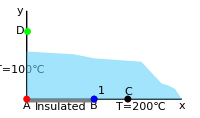

```mathematica
Graphics[{{Line[{{0,0},{0,1.3}}]},{Line[{{0,0},{2.3,0}}]},{Gray,Rectangle[{0,-0.05},{1,0}]},{kru,Opacity[0.6],Polygon[{{0,0},{2.3,0},{2.2,0.15},{2.1,0.2},{2,0.23},{1.7,0.55},{1,0.6},{0.7,0.66},{0,0.7},{0,0}}]},{Text[Style["T=200℃",Medium],{1.7,-0.12}]},{Text[Style["Insulated",Medium],{0.5,-0.12}]},{Text[Style["x",Medium],{2.3,-0.1}]},{Text[Style["y",Medium],{-0.1,1.3}]},{EdgeForm[Directive[Black]],innerbw,Disk[{1,0},0.04]},{Text[Style["1",Medium],{1.1,.12}]},{Red,PointSize[0.025],Point[{0,0}]},{Text[Style[A,Medium],{0,-0.1}]},{Green,PointSize[0.025],Point[{0,1}]},{Text[Style[D,Medium],{-0.1,1}]},{Blue,PointSize[0.025],Point[{1,0}]},{Text[Style[B,Medium],{1,-0.1}]},{Black,PointSize[0.025],Point[{1.5,0}]},{Text[Style[C,Medium],{1.5,0.1}]},{Text[Style["T=100℃",Medium],{-0.1,0.43},Automatic,{0.01,1.0}]}},ImageSize->200]
```

The problem hints that example 4 may be useful. Example 4 uses the ArcSin function to map a heated environment onto the w-plane. First step is to create a list of sample points

```mathematica
sx={{0,0},{1,0},{1.5,0},{0,1}}
```

{{0,0},{1,0},{1.5,0},{0,1}}

and to define an independent function to plot the sample points

```mathematica
gp[{x_,y_}]={N[Re[ArcSin[(x+I y)]]],N[Im[ArcSin[(x+I y)]]]}
```

{Re[ArcSin[x+(0.+1. ⅈ) y]],Im[ArcSin[x+(0.+1. ⅈ) y]]}

then to display the sample points (uh-oh, look at the third point below)

```mathematica
Thread[gp[ sx]]
```

{{0.,0.},{1.5708,0.},{1.5708,-0.962424},{0.,0.881374}}

then to plot the ArcSin function, which looks pretty ragged with its drooping flagstaff.

```mathematica
d2=DiscretizeRegion@ImplicitRegion[0<x≤1.5∧0<y≤20,{x,y}];
ParametricPlot[ReIm[ArcSin[(x+ ⅈ y)]],{x,y}∈d2,PlotRange->{{-1,3},{-1.5,4}},Frame->False,Axes->True,ImageSize->200,AspectRatio->Automatic,Epilog->{{Gray,Rectangle[{0,-0.1},{1.57,0}]},{Red,PointSize[0.025],Point[{0,0}]},{Text[Style[A,Medium],{0,-0.3}]},{Green,PointSize[0.025],Point[{0,0.88}]},{Text[Style[D,Medium],{-0.2,0.88}]},{Blue,PointSize[0.025],Point[{1.57,0}]},{Text[Style[B,Medium],{1.68,-0.2}]},{Black,PointSize[0.025],Point[{1.57,-0.96}]},{Text[Style[C,Medium],{1.7,-1.06}]}}]
```

-Graphics-

This does not look good. The x-axis beyond point B is being mapped negatively down the flagstaff. This is not what example 4 led me to expect. How can this possibly work?

At the Digital Library of Mathematical Functions (https://dlmf.nist.gov/4.23#E16) I found this:

```mathematica
arcsin=-ⅈ Log[((1-(x+I y)^2)^0.5+ⅈ (x+I y))]
```

which I guess means that I have to take some care if I want to invert the sine function in the complex domain. So I will re-do the plot using this new information.

```mathematica
d2=DiscretizeRegion@ImplicitRegion[0<x≤80∧0<y≤100,{x,y}];
sx={{0.001,0.001},{1,0},{1.5,0.001},{0.001,1}}
gq[{x_,y_}]={N[Re[-ⅈ Log[((1-(x+I y)^2)^0.5+ⅈ (x+I y))]]],N[Im[-ⅈ Log[((1-(x+I y)^2)^0.5+ⅈ (x+I y))]]]}
Thread[gq[ sx]]
ParametricPlot[ReIm[-ⅈ Log[((1-(x+I y)^2)^0.5+ⅈ (x+I y))]],{x,y}∈d2,PlotRange->{{-3,2},{-1,6}},Frame->False,Axes->True,ImageSize->200,AspectRatio->Automatic,Epilog->{{Gray,Rectangle[{0,-0.1},{1.57,0}]},{Red,PointSize[0.025],Point[{0.001,0.001}]},{Text[Style[A,Medium],{0,-0.3}]},{Green,PointSize[0.025],Point[{0,0.88}]},{Text[Style[D,Medium],{-0.2,0.88}]},{Blue,PointSize[0.025],Point[{1.57,0}]},{Text[Style[B,Medium],{1.68,-0.2}]},{Black,PointSize[0.025],Point[{1.57,0.96}]},{Text[Style[C,Medium],{1.25,1.06}]}}]
```

{{0.001,0.001},{1,0},{1.5,0.001},{0.001,1}}

{Im[Log[(1.-1. (x+(0.+1. ⅈ) y)^2)^0.5+(0.+1. ⅈ) (x+(0.+1. ⅈ) y)]],-1. Re[Log[(1.-1. (x+(0.+1. ⅈ) y)^2)^0.5+(0.+1. ⅈ) (x+(0.+1. ⅈ) y)]]}

{{0.001,0.001},{1.5708,0.},{1.5699,0.962424},{0.000707107,0.881374}}

-Graphics-

Okay, this looks better. Since the test points are the same as before except for the sign of the v value of point C, I will use the first instantiation of the ArcSine plot, and consider this one a visual correction. Just for clarity, D-A is at 100℃, A-B is insulated, and B-C is at 200℃. Since they are  parallel in the w-plane, it is like a calculation for parallel plates. I don’t think there can be two function coefficent terms, and A is located at zero, which I think zaps it, leaving the field open for B. So the calculation would be

```mathematica
Solve[a 0+b==100&&a π/2+b==200,{a,b}]
```

{{a→200/π,b→100}}

Under the reasoning I just used, the π/2 in the above set refers to the position of B, not to the angle of B-C with the u-axis (also equal to π/2). The equation for Φ then would be

```mathematica
100+200/π Arg[y/x]
```

in the w-plane. But the solution needs to be referred back to the z-plane where it started, so the simple Arg has to be embroidered to express the mapping, I think by writing

```mathematica
100+200/π ArcSin[z]
```

In the text answer this expression is

```mathematica
Re[F[z]]=100+200/π Re[ArcSin[z]]
```

And I assume it is written this way to make clear that although it has two parts, it is not a complex potential.